α

4/25

0

2 Vinf (4/25 √(1-(1-2 x)^2)+α/(√(1-(1-2 x)^2))+((1-2 x) α)/(√(1-(1-2 x)^2)))

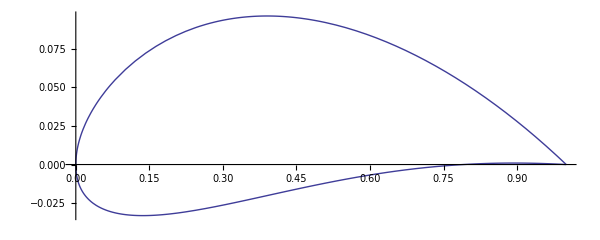

```mathematica
(* Problem 1 *)
eps=4/100;
p=5/10;
c=1;
τ=12/100;
(*α=4 π/180;*)
T[x_]=10 τ c(0.2969 √(x/c)-0.126(x/c)-0.3537(x/c)^2+0.2843(x/c)^3-0.1015(x/c)^4);
Y[x_]=Piecewise[{{(eps x)/p^2(2 p - x/c), 0 ≤ x/c ≤ p },{(eps(c-x))/(1-p)^2(1+x/c-2p) ,p < x/c ≤ 1 }}];
s[θ_]=Simplify[D[Y[x],x]/.x->c/2(1-Cos[θ])];
A0[α_]=Simplify[α-1/π Integrate[s[θ],{θ,0,π}]]
A1=Simplify[2/π Integrate[Cos[θ]s[θ],{θ,0,π}]]
Am[m_]=Assuming[m∈Integers,Simplify[2/π Integrate[Cos[m θ]s[θ],{θ,0,π}]]]
g[θ_,α_]=Simplify[2 Vinf(A0[α](1+Cos[θ])/Sin[θ]+A1 Sin[θ]+Sum[Am[n],{n,2,∞}])];
gx[x_,α_]=g[ArcCos[1-2 x/c],α]
(* Plot airfoil *)
Plot[Y[x]+{T[x]/2,-T[x]/2},{x,0,1},AspectRatio->Automatic,ImageSize->600]
```

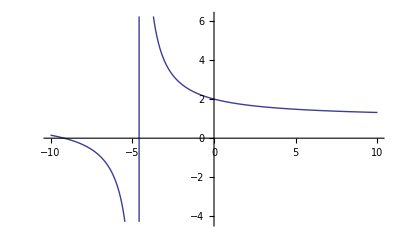

```mathematica
Plot[(4/25+α π/180)/(2/25+α π/180),{α,-10,10}]
```

```mathematica
(* Plot Cp *)
eps=10^-14;
(* thickness: *)
F[x_,xp_]=Vinf/(2π)Integrate[D[T[xp],xp]/(x-xp),xp];
ut[x_]=F[x,1]-F[x,x+eps]+F[x,x-eps]-F[x,0];
vtPlus[x_]=1/2 Vinf D[T[x],x];
vtMinus[x_]=-vtPlus[x];

(* camber: *)
ucPlus[x_,α_]=1/2 gx[x,α];
ucMinus[x_,α_]=-ucPlus[x,α];
G[x_,xp_,α_]=Simplify[-1/(2π)Integrate[gx[xp,α] 1/(x-xp),xp]];
vc[x_,α_]=Limit[G[x,xp+1,α]-G[x,xp+x+eps,α]+G[x,xp+x-eps,α]-G[x,xp+0,α],xp->0];
```

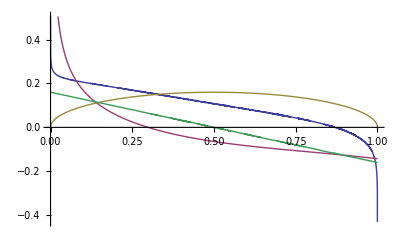

```mathematica
Plot[{ut[x]/Vinf,vtPlus[x]/Vinf,ucPlus[x,0]/Vinf,vc[x,0]/Vinf},{x,0,1}]
CpU[x_,α_]=1-((vtPlus[x]+vc[x,α])^2-(ut[x]+ucPlus[x,α])^2)/Vinf^2;
CpL[x_,α_]=1-((vtMinus[x]+vc[x,α])^2+(ut[x]+ucMinus[x,α])^2)/Vinf^2;
Manipulate[Plot[{CpU[x,α π/180],CpL[x,α π/180]},{x,0,1}],{α,-10,10}]
```

```mathematica
Cl=Assuming[0<p<1,Simplify[2π(A0+A1/2)]];
Cmac=Assuming[0<p<1,Simplify[-π/4(A1-Am[2])]];
xcp=Assuming[0<p<1,Simplify[c/4((A0+A1-1/2 Am[2])/(A0+1/2 A1))]];
```

```mathematica
Integrate[(p-1/2(1-Cos[θp])),θp]
Integrate[Cos[m θp](p-1/2(1-Cos[θp])),θp]
```

-θp/2+p θp+Sin[θp]/2

Sin[(-1+m) θp]/(4 (-1+m))-Sin[m θp]/(2 m)+(p Sin[m θp])/m+Sin[(1+m) θp]/(4 (1+m))